```mathematica
fftSize=10000;
lfactor=2 10^-4;

Manipulate[
Grid[{{Style["Frequency:"<>ToString[freqs2T[[file]]]<>" Hz + 540 Hz",Black,24],SpanFromLeft},

{ListLinePlot[{
lfactor readMyFile[laserfiles2T[[file]],2][[start;;start+segSize]],(* laser *)
-2+readMyFile[nervefiles2T[[file]],2][[start;;start+segSize]]},(* nerve *)
FrameLabel->{"time [s]","Amplitude [nm/mV]"}],

ListLinePlot[{MapAt[1.0 lfactor #&,fourier[readMyFile[laserfiles2T[[file]],2][[start;;start+fftSize]],sRate,1000][[3;;]],{All,2}],
-.3+fourier[readMyFile[nervefiles2T[[file]],2][[start;;start+fftSize]],sRate,1000][[3;;]]},FrameLabel->{"Frequency [Hz]","Amplitude [nm/mV]"},Epilog->Inset[LineLegend[{ColorData[97,1],ColorData[97,2]},Style[#,16,Black]&/@{"Laser","Nerve"}],Scaled[{0.8,0.8}]]]}}],

{{file,30},1,Length@freqs2T,1},{{start,5000,"stimulus amplitude"},1000,40000,5000},{{segSize,500},100,10000},Paneled->False,ControlPlacement->Top]
```

```mathematica
sRate/360.
```

55.5556

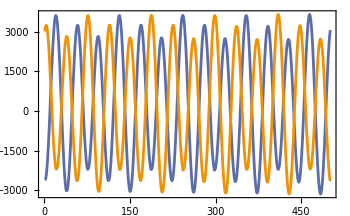

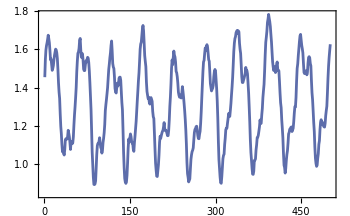

```mathematica
ListLinePlot[{readMyFile[laserfiles2T[[30]],2][[5000;;5000+500]],
readMyFile[laserfiles2T[[30]],2][[5055;;5055+500]]}]
ListLinePlot[{readMyFile[nervefiles2T[[30]],2][[5000;;5000+500]]+
readMyFile[nervefiles2T[[30]],2][[5055;;5055+500]]}]
```